```mathematica
pdf[a_, b_, x_] = PDF[BetaDistribution[a, b], x]
cdf[a_, b_, x_] = CDF[BetaDistribution[a, b], x]
mean[a_, b_] = Mean[BetaDistribution[a, b]]
aqm[a_, b_] = StandardDeviation[BetaDistribution[a, b]]
disp[a_, b_] = aqm[a,b]^2
plot[f_, {x_, xmin_, xmax_}] = Plot[f, {x, xmin, xmax}, PlotLegends->Automatic]
count = 10000
```

Piecewise[{{((1-x)^(-1+b) x^(-1+a))/Beta[a,b], 0<x<1}, {0, True}}]

Piecewise[{{BetaRegularized[x,a,b], 0<x<1}, {1, x≥1}, {0, True}}]

a/(a+b)

(√a √b)/((a+b) √(1+a+b))

(a b)/((a+b)^2 (1+a+b))

Plot::plln: Limiting value xmin in {x,xmin,xmax} is not a machine-sized real number.

Plot[f,{x,xmin,xmax},PlotLegends→Automatic]

10000

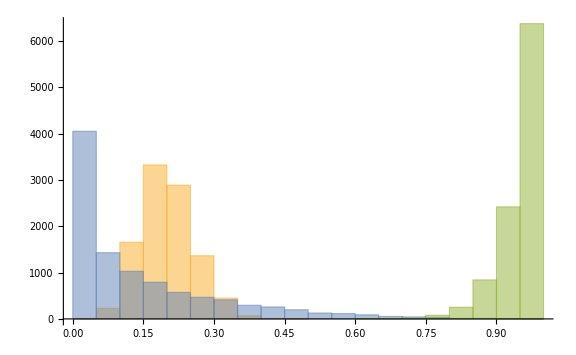

```mathematica
Table[{a[i]=RandomVariate[BetaDistribution[10, 40]],b[i]=RandomVariate[BetaDistribution[1/2, 3]],c[i]=RandomVariate[BetaDistribution[20, 1]]},{i,count}];DownValues[a]; DownValues[b]; DownValues[c];Histogram[{ReleaseHold[First/@DownValues[a]], ReleaseHold[First/@DownValues[b]], ReleaseHold[First/@DownValues[c]]}, ImageSize->Large, LegendAppearance->"Row"]
```

```mathematica
Mean[Table[a[i], {i, count}]]; Mean[Table[b[i], {i, count}]]
```

0.144751

```mathematica
Variance[Table[a[i], {i, count}]]
```

0.00313983

```mathematica
Means = {Mean[Table[a[i], {i, count}]], Mean[Table[b[i], {i, count}]], Mean[Table[c[i], {i, count}]]}
```

{0.200441,0.144751,0.951885}

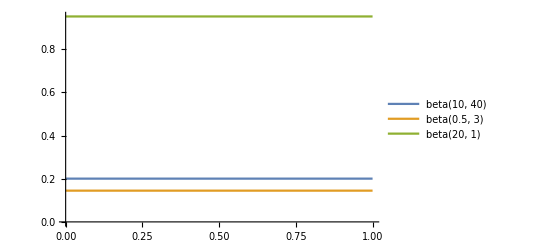

```mathematica
Plot[Means, {x, 0, 1}, PlotLegends -> {"beta(10, 40)", "beta(0.5, 3)", "beta(20, 1)"}]
```

```mathematica
Variances = {Variance[Table[a[i], {i, count}]], Variance[Table[b[i], {i, count}]], Variance[Table[c[i], {i, count}]]}
```

{0.00313983,0.0272996,0.00206262}

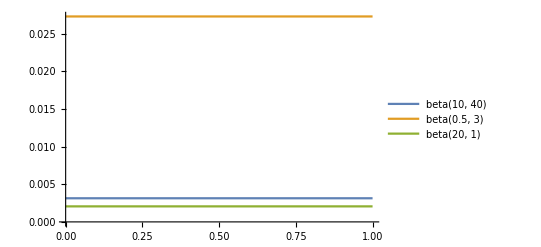

```mathematica
Plot[Variances, {x, 0, 1}, PlotLegends -> {"beta(10, 40)", "beta(0.5, 3)", "beta(20, 1)"}]
```

```mathematica
aa = RandomVariate[BetaDistribution[10, 40], count]; aa = Sort[aa];
ab = RandomVariate[BetaDistribution[1/2, 3], count]; ab = Sort[ab];
ac = RandomVariate[BetaDistribution[20, 1], count]; ac = Sort[ac];
```

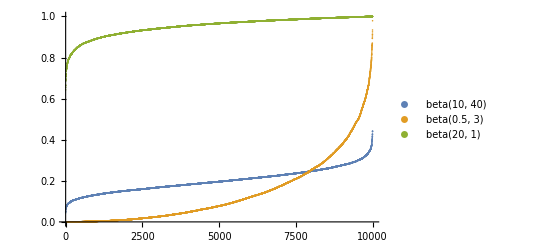

```mathematica
ListPlot[{aa, ab,ac}, PlotLegends -> {"beta(10, 40)", "beta(0.5, 3)", "beta(20, 1)"}]
```

```mathematica
aMeans = {Mean[aa], Mean[ab], Mean[ac]}
```

{0.200378,0.140589,0.952375}

```mathematica
aVariance = {Variance[aa], Variance[ab], Variance[ac]}
```

{0.00309873,0.0267584,0.00208348}

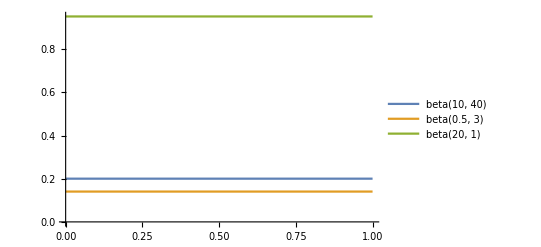

```mathematica
Plot[aMeans, {x, 0, 1}, PlotLegends -> {"beta(10, 40)", "beta(0.5, 3)", "beta(20, 1)"}]
```

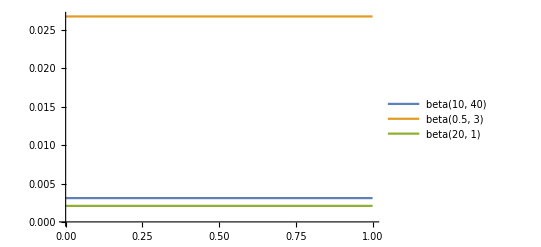

```mathematica
Plot[aVariance, {x, 0, 1}, PlotLegends -> {"beta(10, 40)", "beta(0.5, 3)", "beta(20, 1)"}]
```

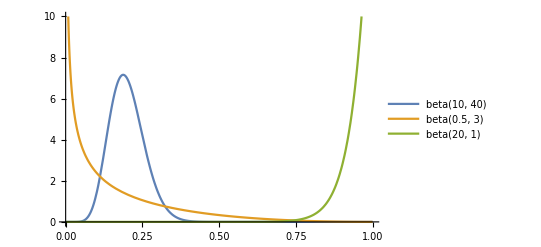

```mathematica
Plot[{pdf[10, 40, x], pdf[0.5, 3, x], pdf[20,1, x]}, {x, 0, 1} , PlotLegends -> {"beta(10, 40)", "beta(0.5, 3)", "beta(20, 1)"}, PlotRange->{Full, {0, 10}}]
```

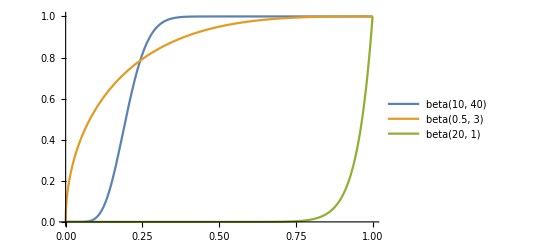

```mathematica
Plot[{cdf[10, 40, x], cdf[0.5, 3, x], cdf[20,1, x]}, {x, 0, 1} , PlotLegends -> {"beta(10, 40)", "beta(0.5, 3)", "beta(20, 1)"}, PlotRange->{Full, {0, 1}}]
```

```mathematica
Mean[BetaDistribution[10, 40]]
```

1/5

```mathematica
Mean[BetaDistribution[1/2, 3]]
```

1/7

```mathematica
Mean[BetaDistribution[20, 1]]
```

20/21

```mathematica
Variance[BetaDistribution[10, 40]]
```

4/1275

```mathematica
Variance[BetaDistribution[1/2, 3]]
```

4/147

```mathematica
Variance[BetaDistribution[20, 1]]
```

10/4851